```mathematica
IsGood[n_]:=With[{all=Map[First, FactorInteger[n]]},Intersection[all,{2,3,5}]==all]
```

```mathematica
Select[Range[1000],IsGood[#]&]
```

{2,3,4,5,6,8,9,10,12,15,16,18,20,24,25,27,30,32,36,40,45,48,50,54,60,64,72,75,80,81,90,96,100,108,120,125,128,135,144,150,160,162,180,192,200,216,225,240,243,250,256,270,288,300,320,324,360,375,384,400,405,432,450,480,486,500,512,540,576,600,625,640,648,675,720,729,750,768,800,810,864,900,960,972,1000}

```mathematica
FindORZero[l_,p_]:=Block[{result},
result=Select[l,#[[1]]==p&];
If[result=={},0,result[[1,2]]]
]
```

```mathematica
FindORZero[{{2,3},{3,10}},2]
```

3

```mathematica
MatrixPlot[Table[ToVector[FactorInteger[k]],{k,Select[Range[1000],IsGood[#]&]}], ImageSize->100]
```

-Graphics-

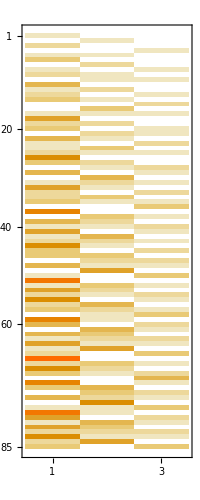

```mathematica
Rotate[,Pi/2]
```

```mathematica
TableForm[Table[ToVector[FactorInteger[k]],{k,Select[Range[1000],IsGood[#]&]}], TableDepth->1]
```

{0,0,1}
{0,1,0}
{0,0,2}
{1,0,0}
{0,1,1}
{0,0,3}
{0,2,0}
{1,0,1}
{0,1,2}
{1,1,0}
{0,0,4}
{0,2,1}
{1,0,2}
{0,1,3}
{2,0,0}
{0,3,0}
{1,1,1}
{0,0,5}
{0,2,2}
{1,0,3}
{1,2,0}
{0,1,4}
{2,0,1}
{0,3,1}
{1,1,2}
{0,0,6}
{0,2,3}
{2,1,0}
{1,0,4}
{0,4,0}
{1,2,1}
{0,1,5}
{2,0,2}
{0,3,2}
{1,1,3}
{3,0,0}
{0,0,7}
{1,3,0}
{0,2,4}
{2,1,1}
{1,0,5}
{0,4,1}
{1,2,2}
{0,1,6}
{2,0,3}
{0,3,3}
{2,2,0}
{1,1,4}
{0,5,0}
{3,0,1}
{0,0,8}
{1,3,1}
{0,2,5}
{2,1,2}
{1,0,6}
{0,4,2}
{1,2,3}
{3,1,0}
{0,1,7}
{2,0,4}
{1,4,0}
{0,3,4}
{2,2,1}
{1,1,5}
{0,5,1}
{3,0,2}
{0,0,9}
{1,3,2}
{0,2,6}
{2,1,3}
{4,0,0}
{1,0,7}
{0,4,3}
{2,3,0}
{1,2,4}
{0,6,0}
{3,1,1}
{0,1,8}
{2,0,5}
{1,4,1}
{0,3,5}
{2,2,2}
{1,1,6}
{0,5,2}
{3,0,3}

```mathematica
Table[k,{k,Select[Range[1000],IsGood[#]&]}]
```

{2,3,4,5,6,8,9,10,12,15,16,18,20,24,25,27,30,32,36,40,45,48,50,54,60,64,72,75,80,81,90,96,100,108,120,125,128,135,144,150,160,162,180,192,200,216,225,240,243,250,256,270,288,300,320,324,360,375,384,400,405,432,450,480,486,500,512,540,576,600,625,640,648,675,720,729,750,768,800,810,864,900,960,972,1000}